```mathematica
Clear["context`*"]
U3γ={{Cos[γ],Sin[γ],0},{-Sin[γ],Cos[γ],0},{0,0,1}};
U1β={{1,0,0},{0,Cos[β],Sin[β]},{0,-Sin[β],Cos[β]}};
U3α={{Cos[α],Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};

U=FullSimplify[U3γ.U1β.U3α,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
MatrixForm@U
(*Ui=Inverse[U];
Ui=FullSimplify[Ui,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
MatrixForm@Ui
FullSimplify[Ui.U,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]*)
Ut=Uᵀ
FullSimplify[Ut.U,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
```

{{Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ],Cos[γ] Sin[α]+Cos[α] Cos[β] Sin[γ],Sin[β] Sin[γ]},{-Cos[β] Cos[γ] Sin[α]-Cos[α] Sin[γ],Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ],Cos[γ] Sin[β]},{Sin[α] Sin[β],-Cos[α] Sin[β],Cos[β]}}

(Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ] | Cos[γ] Sin[α]+Cos[α] Cos[β] Sin[γ] | Sin[β] Sin[γ]
-Cos[β] Cos[γ] Sin[α]-Cos[α] Sin[γ] | Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ] | Cos[γ] Sin[β]
Sin[α] Sin[β] | -Cos[α] Sin[β] | Cos[β])

{{Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ],-Cos[β] Cos[γ] Sin[α]-Cos[α] Sin[γ],Sin[α] Sin[β]},{Cos[γ] Sin[α]+Cos[α] Cos[β] Sin[γ],Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ],-Cos[α] Sin[β]},{Sin[β] Sin[γ],Cos[γ] Sin[β],Cos[β]}}

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Clear["context`*"]

U3γ={{Cos[γ],Sin[γ],0},{-Sin[γ],Cos[γ],0},{0,0,1}};
U1β={{1,0,0},{0,Cos[β],Sin[β]},{0,-Sin[β],Cos[β]}};
U3α={{Cos[α],Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};
U=FullSimplify[U3γ.U1β.U3α,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}];
Ut=Uᵀ;
FullSimplify[U.Ut,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}];

zp={0,0,1};yp={0,1,0};
xp={1,0,0};u={0,0,1};
z=Ut.zp;
y=Ut.yp;
x=Ut.xp;
f=-3/2 κ ((u.z)^2 Δp2+(u.x)^2 Δv12+(u.y)^2 Δv22);
f=FullSimplify[f,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
FullSimplify[D[f,α],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
FullSimplify[D[f,β],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
FullSimplify[D[f,γ],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
Print[Style["*********************************",18,Red]]
f1=FullSimplify[f/.{Δv12->Δv2,Δv22->Δv2},Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
FullSimplify[D[f1,β],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
FullSimplify[D[%,β],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
(*FullSimplify[%/.{Δv12->Δv2,Δv22->Δv2},Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]*)
FullSimplify[D[f1,γ],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]
(*FullSimplify[%/.{Δv12->Δv2,Δv22->Δv2},Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}]*)
```

-3/2 κ (Δp2 Cos[β]^2+Sin[β]^2 (Δv22 Cos[γ]^2+Δv12 Sin[γ]^2))

0

3 κ Cos[β] Sin[β] (Δp2-Δv22 Cos[γ]^2-Δv12 Sin[γ]^2)

3 (-Δv12+Δv22) κ Cos[γ] Sin[β]^2 Sin[γ]

*********************************

-3/4 κ (Δp2+Δv2+(Δp2-Δv2) Cos[2 β])

3 (Δp2-Δv2) κ Cos[β] Sin[β]

3 (Δp2-Δv2) κ Cos[2 β]

0

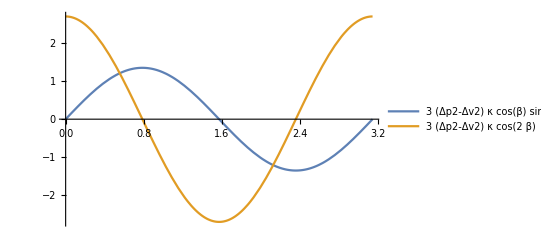

```mathematica
Clear["context`*"]
Δp2=1;Δv2=0.1 Δp2;κ=1;
Plot[{3 (Δp2-Δv2) κ Cos[β] Sin[β],3 (Δp2-Δv2) κ Cos[2 β]},{β,0,π},PlotLegends->"Expressions"]
Clear[Δp2,Δv2]
```

```mathematica
Clear["context`*"]

U3γ={{Cos[γ],Sin[γ],0},{-Sin[γ],Cos[γ],0},{0,0,1}};
U1β={{1,0,0},{0,Cos[β],Sin[β]},{0,-Sin[β],Cos[β]}};
U3α={{Cos[α],Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};
U=FullSimplify[U3γ.U1β.U3α,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}];
Ut=Uᵀ;
FullSimplify[U.Ut,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π}];

zR={0,0,1};yR={0,1,0};
xR={1,0,0};u={0,0,1};
z=Ut.zR;
y=Ut.yR;
x=Ut.xR;
f=1/2 (ηp-ηv) ((u.z)^2 Δp2+(u.x)^2 Δv12+(u.y)^2 Δv22);
f=FullSimplify[f,Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π&&{ηp,ηv}∈Reals}]
FullSimplify[D[f,α],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π&&{ηp,ηv}∈Reals}]
FullSimplify[D[f,β],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π&&{ηp,ηv}∈Reals}]
FullSimplify[D[f,γ],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π&&{ηp,ηv}∈Reals}]
Print[Style["*********************************",18,Red]]
f1=FullSimplify[f/.{Δv12->Δv2,Δv22->Δv2},Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π&&{ηp,ηv}∈Reals}]
FullSimplify[D[f1,β],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π&&{ηp,ηv}∈Reals}]
FullSimplify[D[%,β],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π&&{ηp,ηv}∈Reals}]

FullSimplify[D[f1,γ],Assumptions->{α∈Reals&&β∈Reals&&γ∈Reals&&κ∈Reals&&α≥0&&α≤2 π&&γ≥0&&γ≤2 π&&β≥0&&β≤π&&{ηp,ηv}∈Reals}]
```

1/2 (ηp-ηv) (Δp2 Cos[β]^2+Sin[β]^2 (Δv22 Cos[γ]^2+Δv12 Sin[γ]^2))

0

(ηp-ηv) Cos[β] Sin[β] (-Δp2+Δv22 Cos[γ]^2+Δv12 Sin[γ]^2)

(Δv12-Δv22) (ηp-ηv) Cos[γ] Sin[β]^2 Sin[γ]

*********************************

1/4 (ηp-ηv) (Δp2+Δv2+(Δp2-Δv2) Cos[2 β])

-(Δp2-Δv2) (ηp-ηv) Cos[β] Sin[β]

-(Δp2-Δv2) (ηp-ηv) Cos[2 β]

0

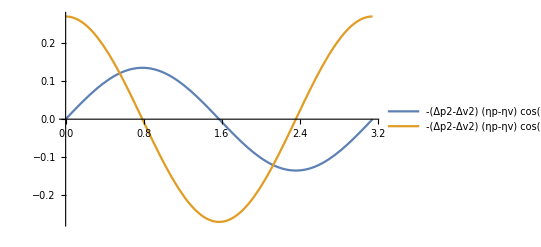

```mathematica
Clear["context`*"]
Δp2=1;Δv2=0.1 Δp2;
(*ηp=-1;ηv=0.5 ηp;*)
ηv=1;ηp=0.7 ηv;
Plot[{-(Δp2-Δv2) (ηp-ηv) Cos[β] Sin[β],-(Δp2-Δv2) (ηp-ηv) Cos[2 β]},{β,0,π},PlotLegends->"Expressions"]
Clear[Δp2,Δv2]
```